Instructions:
1.  Execute Cells 1 through 7  in that  order (twice each if you want to  get rid of  
     annoying warning messages) to initialize all necessary modules. 
     Shortcut for Mathematica 4.0 or 5.0  users: select 
     Kernel ->Evaluation->Evaluate Initialization  
     To check individual cells, run test code (blue) for that cell only.
2.  Cell 8 contains the driver program script for the  bridge truss example.  
     Run by selecting the cell and executing.
3.  Execute Cell 8A to generate deformed shape plot frames.   Animate by double
     clicking one of the frames.  Animation speed may be controlled  by the playback
     button controls on the left side of the bottom window bar.
4.  If the plots produced by running a program appear too small,  click 
     on the top  one  (only)  with the mouse,  grap a corner "handle" and enlarge it.  
     Then rerun  the program. 
5.  To prepare a problem driver for the homework, open up a new cell, say 9,
     and write the script using Cell 8 as "template".   Don't try to do the whole
     thing at once.  Write a few statements and run the script up to that point
     (before running don't forget to have initialized Cells 1-7 as indicated above).
     Examine output and resolve error messages (if any) before proceeding.

Cell 0.  Mathematica version-dependent settings (to get plots displayed correctly)

```mathematica
DisplayChannel=$DisplayFunction;
If [$VersionNumber>=6.0, DisplayChannel=Print]; 
  (* fix for Mathematica 6 & later *)
  
Off[General::"spell1"];
```

Cell 1.  Assembly module for space truss structure.  The element stiffness module that
supports the assembler has been described in Chapter 20.

```mathematica
SpaceTrussMasterStiffness[nodxyz_,elenod_,
   elemat_,elefab_,prcopt_]:=Module[
  {numele=Length[elenod],numnod=Length[nodxyz],neldof,
  e,eftab,ni,nj,i,j,ii,jj,ncoor,Em,A,options,Ke,K},
  K=Table[0,{3*numnod},{3*numnod}];
  For [e=1, e<=numele, e++, {ni,nj}=elenod[[e]]; 
      eftab={3*ni-2,3*ni-1,3*ni,3*nj-2,3*nj-1,3*nj}; 
      ncoor={nodxyz[[ni]],nodxyz[[nj]]};         
      Em=elemat[[e]]; A=elefab[[e]]; options=prcopt;  
      Ke=SpaceBar2Stiffness[ncoor,Em,A,options];
      neldof=Length[Ke];
      For [i=1, i<=neldof, i++, ii=eftab[[i]];
          For [j=i, j<=neldof, j++, jj=eftab[[j]];
              K[[jj,ii]]=K[[ii,jj]]+=Ke[[i,j]] ];
          ];
      ]; Return[K];
  ];
SpaceBar2Stiffness[ncoor_,Em_,A_,options_]:=Module[
  {x1,x2,y1,y2,z1,z2,x21,y21,z21,EA,numer,L,LL,LLL,Ke}, 
  {{x1,y1,z1},{x2,y2,z2}}=ncoor; {x21,y21,z21}={x2-x1,y2-y1,z2-z1};
  EA=Em*A; {numer}=options;  LL=x21^2+y21^2+z21^2; L=Sqrt[LL];
  If [numer,{x21,y21,z21,EA,LL,L}=N[{x21,y21,z21,EA,LL,L}]];
  If [!numer, L=PowerExpand[L]]; LLL=Simplify[LL*L];
  Ke=(Em*A/LLL)*
     {{ x21*x21, x21*y21, x21*z21,-x21*x21,-x21*y21,-x21*z21},
      { y21*x21, y21*y21, y21*z21,-y21*x21,-y21*y21,-y21*z21},
      { z21*x21, z21*y21, z21*z21,-z21*x21,-z21*y21,-z21*z21},
      {-x21*x21,-x21*y21,-x21*z21, x21*x21, x21*y21, x21*z21},
      {-y21*x21,-y21*y21,-y21*z21, y21*x21, y21*y21, y21*z21},
      {-z21*x21,-z21*y21,-z21*z21, z21*x21, z21*y21, z21*z21}};
  Return[Ke]];
  
ClearAll[nodxyz,elemat,elefab,eleopt];
nodxyz={{0,0,0},{10,0,0},{10,10,0}};
elenod= {{1,2},{2,3},{1,3}};
elemat= Table[100,{3}]; elefab= {1,1/2,2*Sqrt[2]}; prcopt= {False};
K=SpaceTrussMasterStiffness[nodxyz,elenod,elemat,elefab,prcopt];
Print["Master Stiffness of Example Truss in 3D:\n",K//MatrixForm];
Print["eigs of K:",Chop[Eigenvalues[N[K]]]];
```

Master Stiffness of Example Truss in 3D:
(20 | 10 | 0 | -10 | 0 | 0 | -10 | -10 | 0
10 | 10 | 0 | 0 | 0 | 0 | -10 | -10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-10 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 0 | 0 | -5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-10 | -10 | 0 | 0 | 0 | 0 | 10 | 10 | 0
-10 | -10 | 0 | 0 | -5 | 0 | 10 | 15 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

eigs of K:{45.3577,16.7403,7.902,0,0,0,0,0,0}

Cell 2.  These modules apply the displacement boundary conditions by modifying the force
vector and the master stiffness matrix.  This implementation of ModifyNodeForces
handles nonzero prescribed displacements.

```mathematica
ModifiedMasterStiffness[nodtag_,K_] := Module[
  {i,j,k,n=Length[K],pdof,np,Kmod=K},
  pdof=PrescDisplacementDOFTags[nodtag]; np=Length[pdof];
  For [k=1,k<=np,k++, i=pdof[[k]]; 
      For [j=1,j<=n,j++, Kmod[[i,j]]=Kmod[[j,i]]=0];
      Kmod[[i,i]]=1]; 
  Return[Kmod]];  
  
ModifiedNodeForces[nodtag_,nodval_,K_,f_]:= Module[
  {i,j,k,n=Length[K],pdof,pval,np,d,c,fmod=f},
  pdof=PrescDisplacementDOFTags[nodtag]; np=Length[pdof];
  pval=PrescDisplacementDOFValues[nodtag,nodval]; c=Table[1,{n}]; 
  For [k=1,k<=np,k++, i=pdof[[k]]; c[[i]]=0];
  For [k=1,k<=np,k++, i=pdof[[k]]; d=pval[[k]]; 
      fmod[[i]]=d; If [d==0, Continue[]];
      For [j=1,j<=n,j++, fmod[[j]]-=K[[i,j]]*c[[j]]*d]; 
      ];  
  Return[fmod]];
  
PrescDisplacementDOFTags[nodtag_]:= Module [
 {j,n,numnod=Length[nodtag],pdof={},k=0,m},
  For [n=1,n<=numnod,n++, m=Length[nodtag[[n]]];
      For [j=1,j<=m,j++, If [nodtag[[n,j]]>0, 
                AppendTo[pdof,k+j]];
         ]; k+=m;
     ]; Return[pdof]]; 
           
PrescDisplacementDOFValues[nodtag_,nodval_]:= Module [
 {j,n,numnod=Length[nodtag],pval={},k=0,m},
  For [n=1,n<=numnod,n++, m=Length[nodtag[[n]]];
      For [j=1,j<=m,j++, If [nodtag[[n,j]]>0, 
                AppendTo[pval,nodval[[n,j]]]];
         ]; k+=m;
     ]; Return[pval]];

ClearAll[K,f,v1,v2,v4]; Km=Array[K,{6,6}];
Print["Master Stiffness: ",Km//MatrixForm];
nodtag={{1,1},{0,1},{0,0}}; nodval={{v1,v2},{0,v4},{0,0}};
Kmod=ModifiedMasterStiffness[nodtag,Km];
Print["Modified Master Stiffness:",Kmod//MatrixForm];
fm=Array[f,{6}]; Print["Master Force Vector:",fm];
fmod=ModifiedNodeForces[nodtag,nodval,Km,fm];
Print["Modified Force Vector:",fmod//MatrixForm];

(*nodtag= {{0,1,0},{0,0,0},{1,0,1},{0,1,1},{0,0,1}};
nodval=-{{1,2,3},{4,5,6},{7,8,9},{10,11,12},{13,14,15}};
Print[PrescDisplacementDOFTags[nodtag]];
Print[PrescDisplacementDOFValues[nodtag,nodval]];*)
```

Master Stiffness: (K[1,1] | K[1,2] | K[1,3] | K[1,4] | K[1,5] | K[1,6]
K[2,1] | K[2,2] | K[2,3] | K[2,4] | K[2,5] | K[2,6]
K[3,1] | K[3,2] | K[3,3] | K[3,4] | K[3,5] | K[3,6]
K[4,1] | K[4,2] | K[4,3] | K[4,4] | K[4,5] | K[4,6]
K[5,1] | K[5,2] | K[5,3] | K[5,4] | K[5,5] | K[5,6]
K[6,1] | K[6,2] | K[6,3] | K[6,4] | K[6,5] | K[6,6])

Modified Master Stiffness:(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | K[3,3] | 0 | K[3,5] | K[3,6]
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | K[5,3] | 0 | K[5,5] | K[5,6]
0 | 0 | K[6,3] | 0 | K[6,5] | K[6,6])

Master Force Vector:{f[1],f[2],f[3],f[4],f[5],f[6]}

Modified Force Vector:(v1
v2
f[3]-v1 K[1,3]-v2 K[2,3]-v4 K[4,3]
v4
f[5]-v1 K[1,5]-v2 K[2,5]-v4 K[4,5]
f[6]-v1 K[1,6]-v2 K[2,6]-v4 K[4,6])

Cell 3.  Computation of internal forces (axial forces) for all elements of a space truss,
from the computed nodal displacements.

```mathematica
SpaceTrussIntForces[nodxyz_,elenod_,elemat_,elefab_,
  noddis_,prcopt_]:= Module[{  numnod=Length[nodxyz],
  numele=Length[elenod],e,ni,nj,ncoor,Em,A,options,ue,p},
  p=Table[0,{numele}]; 
  For [e=1, e<=numele, e++, {ni,nj}=elenod[[e]]; 
      ncoor={nodxyz[[ni]],nodxyz[[nj]]}; 
      ue=Flatten[{ noddis[[ni]],noddis[[nj]] }];          
      Em=elemat[[e]]; A=elefab[[e]]; options=prcopt; 
      p[[e]]=SpaceBar2IntForce[ncoor,Em,A,ue,options]
      ]; 
  Return[p]];

SpaceBar2IntForce[ncoor_,Em_,A_,ue_,options_]:= Module[ 
 {x1,x2,y1,y2,z1,z2,x21,y21,z21,EA,numer,LL,pe}, 
 {{x1,y1,z1},{x2,y2,z2}}=ncoor; {x21,y21,z21}={x2-x1,y2-y1,z2-z1};
  EA=Em*A; {numer}=options;  LL=x21^2+y21^2+z21^2;
  If [numer,{x21,y21,z21,EA,LL}=N[{x21,y21,z21,EA,LL}]];
  pe=(EA/LL)*(x21*(ue[[4]]-ue[[1]])+y21*(ue[[5]]-ue[[2]])+
             +z21*(ue[[6]]-ue[[3]]));
  Return[pe]]; 
  
SpaceTrussStresses[elefab_,elefor_,prcopt_]:= Module[
 {numele=Length[elefab],e,elesig}, elesig=Table[0,{numele}]; 
  For [e=1, e<=numele, e++, elesig[[e]]=elefor[[e]]/elefab[[e]] ];
  Return[elesig]]; 

ClearAll[nodxyz,elenod,elemat,elefab,noddis];
nodxyz={{0,0,0},{10,0,0},{10,10,0}}; elenod={{1,2},{2,3},{1,3}};
elemat= Table[100,{3}]; elefab= {1,1/2,2*Sqrt[2]};
noddis={{0,0,0}, {0,0,0}, {4/10,-2/10,0}}; prcopt={False};
elefor=SpaceTrussIntForces[nodxyz,elenod,elemat,elefab,noddis,prcopt];
Print["Int Forces of Example Truss:",elefor];
Print["Stresses:",SpaceTrussStresses[elefab,elefor,prcopt]];
```

Int Forces of Example Truss:{0,-1,2 √2}

Stresses:{0,-2,1}

Cell 4 has  groups plot modules that support preprocessing, that is, draw pictures of the FEM model.
Modules to plot loads and BCs removed to keep it short.   PlotSpaceTrussElements draws only the 
element (bars) without any labels. PlotSpaceTrussElementsAndNodes draws elements and nodes, 
and optionally labels them.

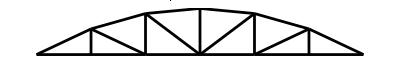

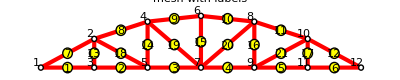

```mathematica
WorldToScreenMatrix[view_]:=Module[{VW={{0,1,0},{0,0,1}},
  Vx,Vy,Vz,Wx,Wy,Wz,xden,yden,Q}, 
  If [Length[view]==2, VW=view];
  If [Length[view]==3, VW[[2]]=view];
  {{Vx,Vy,Vz},{Wx,Wy,Wz}}=VW;
  xden=Sqrt[Wz^2*(Vx^2+Vy^2)-2*Wx*Wz*Vx*Vz-
  2*Wy*Vy*(Wx*Vx+Wz*Vz)+Wy^2*(Vx^2+Vz^2)+Wx^2*(Vy^2+Vz^2)];
  yden=Sqrt[(Wx^2+Wy^2+Wz^2)*(Wz^2*(Vx^2+Vy^2)-2*Wx*Wz*Vx*Vz-
  2*Wy*Vy*(Wx*Vx+Wz*Vz)+Wy^2*(Vx^2+Vz^2)+Wx^2*(Vy^2+Vz^2))];
  Q={{Wz*Vy-Wy*Vz,-Wz*Vx+Wx*Vz,Wy*Vx-Wx*Vy}/xden, 
     {Wy^2*Vx-Wx*Wy*Vy+Wz*(Wz*Vx-Wx*Vz),-Wx*Wy*Vx+Wx^2*Vy+ 
     Wz*(Wz*Vy-Wy*Vz),-Wz*(Wx*Vx+Wy*Vy)+(Wx^2+Wy^2)*Vz}/yden};
  Return[Q]];

PlotSpaceTrussElements[nodxyz_,elenod_,title_,{view_,aspect_,labels_}]:= 
  Module[{numnod=Length[nodxyz],numele=Length[elenod],
  e,n,ni,nj,Q,x,y,xmin,xmax,ymin,ymax,dx,dy,xyc,ar,pbars={}},
  x=y=Table[0,{numnod}]; Q=WorldToScreenMatrix[view];
  For [n=1,n<=numnod,n++, {x[[n]],y[[n]]}=Q.nodxyz[[n]] ];
  {xmin,xmax,ymin,ymax}=N[{Min[x],Max[x],Min[y],Max[y]}];
  {dx,dy}={xmax-xmin,ymax-ymin};
  For [e=1,e<=numele,e++, {ni,nj}=elenod[[e]]; 
       xyc={{x[[ni]],y[[ni]]},{x[[nj]],y[[nj]]}};      
       AppendTo[pbars,Graphics[Line[xyc]]]
      ];
 arat=AspectRatio->Automatic; If [aspect>0, arat=AspectRatio->aspect];
 If [aspect==0&&dx>0, arat=AspectRatio->dy/dx];
 Show[Graphics[AbsoluteThickness[2]],
      Graphics[RGBColor[0,0,0]],
      pbars, arat, PlotLabel->title,
      DisplayFunction->DisplayChannel ];
 ClearAll[pbars];
 ];

PlotSpaceTrussElementsAndNodes[nodxyz_,elenod_,title_,
   {view_,aspect_,labels_}]:= Module[{numnod=Length[nodxyz],
  numele=Length[elenod],k=Length[labels],e,n,ni,nj,Q,x,y,xyc,
  xy0,xyn,xmin,xmax,ymin,ymax,elabels,nlabels,fntinfo,
  labnod,frn,fex,fey,labele,fre,fntnam,fntsiz,fntwgt,fntslt,
  black,red,green,blue,yellow,fill,grey,nofill,arat,
  style,dx,dy,dmin,rn,re,ex,ey,elab,nlab,pbars={},
  pecirc={},pelab={},pedisk={},pncirc={},pndisk={},pnlab={} },
  x=y=Table[0,{numnod}]; Q=WorldToScreenMatrix[view];
  {labnod,frn,fex,fey,labele,fre,fntnam,fntsiz,fntwgt,fntslt}=
    {True,0.03,-1.5,0.8,True,0.03,"Times",12,"Plain","Plain"};  
  If [k>=1, nlabels=labels[[1]] ]; 
  If [k>=2, elabels=labels[[2]] ];
  If [k>=3, fntinfo=labels[[3]] ];
  If [Length[nlabels]>=1, labnod=nlabels[[1]] ];
  If [Length[nlabels]>=2, frn=   nlabels[[2]] ];
  If [Length[nlabels]>=3, fex=   nlabels[[3]] ];
  If [Length[nlabels]>=4, fey=   nlabels[[4]] ];
  If [Length[elabels]>=1, labele=elabels[[1]] ];
  If [Length[elabels]>=2, fre=   elabels[[2]] ];
  If [Length[fntinfo]>=1, fntnam=fntinfo[[1]] ];
  If [Length[fntinfo]>=2, fntsiz=fntinfo[[2]] ];
  If [Length[fntinfo]>=3, fntwgt=fntinfo[[3]] ];
  If [Length[fntinfo]>=4, fntslt=fntinfo[[4]] ];
  For [n=1,n<=numnod,n++, {x[[n]],y[[n]]}=Q.nodxyz[[n]] ];
  {xmin,xmax,ymin,ymax}=N[{Min[x],Max[x],Min[y],Max[y]}];
  {dx,dy}={xmax-xmin,ymax-ymin}; dmin=Min[dx,dy];
  rn=frn*dmin; re=fre*dmin;
  style=TextStyle->{FontFamily->fntnam,FontSize-> fntsiz,
                    FontWeight->fntwgt,FontSlant->fntslt};
  For [e=1,e<=numele,e++, {ni,nj}=elenod[[e]]; 
      xyc={{x[[ni]],y[[ni]]},{x[[nj]],y[[nj]]}};
      xy0=(xyc[[1]]+xyc[[2]])/2;
      AppendTo[pbars,Graphics[Line[xyc]]];
      If [labele, elab=ToString[e];
          AppendTo[pedisk, Graphics[Disk[xy0,re]]]; 
          AppendTo[pecirc, Graphics[Circle[xy0,re]]];
          AppendTo[pelab,  Graphics[Text[elab,xy0-{0,0.2*re},style]]]
         ];
      ];
  style=TextStyle->{FontFamily->fntnam,FontSize-> fntsiz,
                    FontWeight->"Bold",FontSlant->"Plain"};
  For [n=1,n<=numnod,n++,  xyn={x[[n]],y[[n]]}; 
      AppendTo[pndisk,  Graphics[Disk[xyn,rn]]];
      AppendTo[pncirc,  Graphics[Circle[xyn,rn]]];
      If [labnod, nlab=ToString[n]; xy0=xyn+{fex,fey}*rn; 
          AppendTo[pnlab, Graphics[Text[nlab,xy0,style]]]];
     ]; 
  {black,red,green,blue,yellow}={RGBColor[0,0,0],RGBColor[1,0,0],
     RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[1,1,0]};
  {nofill,grey,fill}={GrayLevel[0],GrayLevel[.8],GrayLevel[1]};
  arat=AspectRatio->Automatic; 
  If [aspect>0, arat=AspectRatio->aspect];
  If [aspect==0&&dx>0, arat=AspectRatio->dy/dx];
  Show[Graphics[nofill],Graphics[AbsoluteThickness[3]],
       Graphics[red],pbars, Graphics[AbsoluteThickness[1]],
       Graphics[fill],pndisk, Graphics[nofill],pncirc, 
       Graphics[yellow], pedisk, Graphics[nofill], 
       Graphics[black], pecirc, pelab, pnlab,
       arat, PlotLabel->title,
       DisplayFunction->DisplayChannel ];
   ClearAll[pbars,pndisk,pncirc,pedisk,pecirc,pelab];
 ];
 
nodxyz={{0,0,0},{10,5,0},{10,0,0},{20,8,0},{20,0,0},{30,9,0},
       {30,0,0},{40,8,0},{40,0,0},{50,5,0},{50,0,0},{60,0,0}};
nodxyz=N[nodxyz];
elenod={{1,3},{3,5},{5,7},{7,9},{9,11},{11,12},
        {1,2},{2,4},{4,6},{6,8},{8,10},{10,12},
        {2,3},{4,5},{6,7},{8,9},{10,11},
        {2,5},{4,7},{7,8},{9,10}};
view={{0,1,0},{0,0,1}}; 
PlotSpaceTrussElements[nodxyz,elenod,"plain mesh",{view,0,{}}];
labels={{True,0.05,-1.8,1.8},{True,0.10},{"Times",12,"Plain","Italic"}};
PlotSpaceTrussElementsAndNodes[nodxyz,elenod,"mesh with labels",{view,-1,labels}];
```

Cell 5.  Plot modules that support postprocessing.   These are subdivided into Cells 5A and 5C to keep them short.

Cell 5A. PlotSpaceTrussDeformedShape does exactly what it says.  Note: argument amplif can be
a scalar amplification, or a list of amplifications.  If the latter, a sequence of colors is used.

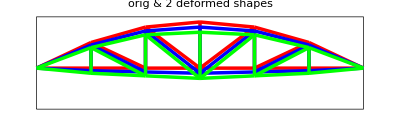

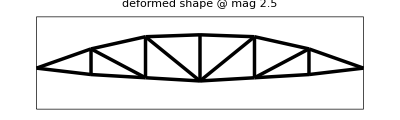

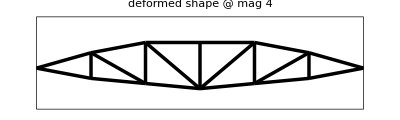

```mathematica
PlotSpaceTrussDeformedShape[nodxyz_,elenod_,noddis_,
    amplif_,box_,title_,{view_,aspect_,colors_}]:= 
  Module[{numnod=Length[nodxyz],numele=Length[elenod],a={},c={},e,k,m,n,
  ni,nj,nf,Q,xbox,ybox,x,y,x0,y0,xmin,xmax,ymin,ymax,dx,dy,xyc,arat,
  black,red,green,blue,yellow,white,fill,grey,nofill,f,pbars={},p={}},
  Q=WorldToScreenMatrix[view]; x=y=Table[0,{numnod}]; nf=Length[box]; 
  If [nf>0, xbox=ybox=Table[0,{nf}]; 
      For [n=1,n<=nf,n++, {xbox[[n]],ybox[[n]]}=Q.box[[n]] ];
      {xmin,xmax,ymin,ymax}=N[{Min[xbox],Max[xbox],Min[ybox],Max[ybox]}] ];      
  If [nf==0,
      For [n=1,n<=numnod,n++, {x[[n]],y[[n]]}=Q.nodxyz[[n]] ];
      {xmin,xmax,ymin,ymax}=N[{Min[x],Max[x],Min[y],Max[y]}] ];
  {dx,dy}={xmax-xmin,ymax-ymin};
  {black,red,green,blue,yellow,white}={RGBColor[0,0,0],RGBColor[1,0,0],
     RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[1,1,0],RGBColor[1,1,1]};
  {nofill,grey,fill}={GrayLevel[0],GrayLevel[.8],GrayLevel[1]};
  arat=AspectRatio->Automatic; 
  If [aspect>0, arat=AspectRatio->aspect];
  If [aspect==0&&dx>0, arat=AspectRatio->dy/dx];
  AppendTo[p,Graphics[AbsoluteThickness[.5]]]; AppendTo[p,Graphics[nofill]];
  enclosingbox={{xmin,ymin},{xmax,ymin},{xmax,ymax},{xmin,ymax},{xmin,ymin}};
  AppendTo[p,Graphics[Line[enclosingbox]]]; 
  AppendTo[p,Graphics[AbsoluteThickness[2.5]]];
  If [Length[amplif]==0,a={amplif},a=amplif];
  If [Length[colors]==0,c={colors},c=colors]; k=Length[c];
  AppendTo[p,Graphics[black]];
  For [m=1,m<=Length[a],m++, f=a[[m]]; color=c[[Min[m,k]]];
       If [color=="black",  AppendTo[p,Graphics[black]]];
       If [color=="red",    AppendTo[p,Graphics[red]]];
       If [color=="blue",   AppendTo[p,Graphics[blue]]];
       If [color=="green",  AppendTo[p,Graphics[green]]];
       If [color=="yellow", AppendTo[p,Graphics[yellow]]];
       If [color=="white",  AppendTo[p,Graphics[white]]];
       For [n=1,n<=numnod,n++, 
           {x[[n]],y[[n]]}=Q.(nodxyz[[n]]+f*noddis[[n]])];
       For [e=1,e<=numele,e++, {ni,nj}=elenod[[e]]; 
            xyc={{x[[ni]],y[[ni]]},{x[[nj]],y[[nj]]}};      
       AppendTo[p,Graphics[Line[xyc] ]]];
      ];
 Show[p, arat, PlotLabel->title, DisplayFunction->DisplayChannel ]; 
 ClearAll[x,y,xbox,ybox,p]; 
 ];
 

nodxyz={{0,0,0},{10,5,0},{10,0,0},{20,8,0},{20,0,0},{30,9,0},
       {30,0,0},{40,8,0},{40,0,0},{50,5,0},{50,0,0},{60,0,0}};
noddis={{0,0,0},{0,-10,0},{0,-10,0},{0,-15,0},{0,-15,0},{0,-20,0},
       {0,-20,0},{0,-15,0},{0,-15,0},{0,-10,0},{0,-10,0},{0,0,0}}/20;
nodxyz=N[nodxyz];
elenod={{1,3},{3,5},{5,7},{7,9},{9,11},{11,12},
        {1,2},{2,4},{4,6},{6,8},{8,10},{10,12},
        {2,3},{4,5},{6,7},{8,9},{10,11},
        {2,5},{4,7},{7,8},{9,10}};
view={{0,1,0},{0,0,1}}; box={{0,-8,0},{60,-8,0},{60,10,0},{0,10,0}};
PlotSpaceTrussDeformedShape[nodxyz,elenod,noddis,{0,1,2},
         box,"orig & 2 deformed shapes",{view,-1,{"red","blue","green"}}]; 
PlotSpaceTrussDeformedShape[nodxyz,elenod,noddis,2.5,box,
         "deformed shape @ mag 2.5",{view,-1,"black"}]; 
PlotSpaceTrussDeformedShape[nodxyz,elenod,noddis,4.0,box,
         "deformed shape @ mag 4",{view,-1,"black"}];
```

Cell 5B. Plot Axial Stress level displays stress level and sign using color: red for tension,
blue for compression, white for zero stress.  A black background is used.

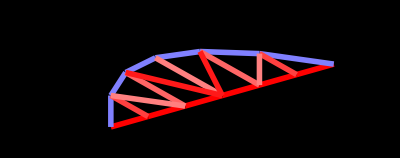

```mathematica
PlotSpaceTrussStresses[nodxyz_,elenod_,elesig_,sigfac_,box_,
      title_,{view_,aspect_,labels_}]:=  Module[
 {numele=Length[elenod],numnod=Length[nodxyz],
  e,n,ni,nj,nc,nf,xyc,x,y,xbox,ybox,xmin,xmax,ymin,ymax,dx,dy,
  smin,smax,fmax,sval,c1,c2,c3,arat,pbox={},pbars={}},
  x=y=Table[0,{numnod}]; Q=WorldToScreenMatrix[view]; nf=Length[box];
  For [n=1,n<=numnod,n++, {x[[n]],y[[n]]}=Q.nodxyz[[n]] ];
  If [nf>0, xbox=ybox=Table[0,{nf}]; 
      For [n=1,n<=nf,n++, {xbox[[n]],ybox[[n]]}=Q.box[[n]] ];
      {xmin,xmax,ymin,ymax}=N[{Min[xbox],Max[xbox],Min[ybox],Max[ybox]}] ];      
  If [nf==0,
      {xmin,xmax,ymin,ymax}=N[{Min[x],Max[x],Min[y],Max[y]}] ];
  {dx,dy}={xmax-xmin,ymax-ymin};
  AppendTo[pbox,Graphics[AbsoluteThickness[.5]]]; 
  AppendTo[pbox,Graphics[GrayLevel[0]]];
  enclosingbox={{xmin,ymin},{xmax,ymin},{xmax,ymax},{xmin,ymax},{xmin,ymin}};
  AppendTo[pbox,Graphics[Line[enclosingbox]]];
  AppendTo[pbox,Graphics[AbsoluteThickness[4]]]; 
  smin=Min[elesig]; smax=Max[elesig]; fmax=Max[Abs[smax],Abs[smin]];
  For [e=1,e<=numele,e++, 
     sval=N[elesig[[e]]*sigfac]; {c1,c2,c3}=LineColor[sval,fmax]; 
     {ni,nj}=elenod[[e]]; xyc={{x[[ni]],y[[ni]]},{x[[nj]],y[[nj]]}};    
     AppendTo[pbars,Graphics[RGBColor[c1,c2,c3]]];
     AppendTo[pbars,Graphics[Line[xyc]]]
     ];
  arat=AspectRatio->Automatic; 
  If [aspect>0, arat=AspectRatio->aspect];
  If [aspect==0&&dx>0, arat=AspectRatio->dy/dx];
  Show[pbox,Graphics[RGBColor[0,0,0]],pbars, 
       Background->GrayLevel[0], arat, PlotLabel->title,
       DisplayFunction->DisplayChannel ];
   ClearAll[pbars,x,y];
 ];

LineColor[f_,fmax_]:= Module[{r,RGBmax={1,0,0},  
   RGBmin={0,0,1}, RGBzero={1,1,1}, RGBout={0,0,0}},
   If [f==0 || fmax==0,   
       Return[RGBzero]];  (* White if f=0 *)
   If [f>fmax || f<-fmax, 
       Return[RGBout ]];  (* Black if outside range *)
   If [f>0, r= N[f/fmax]; 
       Return[r*RGBmax+(1-r)*RGBzero]]; (* positive *)
   If [f<0, r=-N[f/fmax]; 
       Return[r*RGBmin+(1-r)*RGBzero]]; (* negative *)
];

nodxyz={{0,0,0},{10,5,0},{10,0,0},{20,8,0},{20,0,0},{30,9,0},
       {30,0,0},{40,8,0},{40,0,0},{50,5,0},{50,0,0},{60,0,0}};
elenod= {{1,3},{3,5},{5,7},{7,9},{9,11},{11,12},
         {1,2},{2,4},{4,6},{6,8},{8,10},{10,12},
         {2,3},{4,5},{6,7},{8,9},{10,11},
         {2,5},{4,7},{7,8},{9,10}};
elesig={20,20,20,20,20,20,-10,-10,-10,-10,-10,-10,
        15,12,10,12,15,10,18,18,10};
view={{2,1,0},{-3,-1,1}};  box={{0,-4,0},{60,-4,0},{60,10,0},{0,10,0}};
PlotSpaceTrussStresses[nodxyz,elenod,elesig,1,box,
   "axial stress in truss members",{view,0,labels}];
```

Cell 6.  Miscellaneous utilities supporting print output and some array transformations

```mathematica
PrintSpaceTrussNodeCoordinates[nodxyz_,title_,digits_]:= Module[
  {numnod=Length[nodxyz],n,x,y,z,d=6,f=6,tab}, 
  tab=Table[0,{numnod}]; If [Length[digits]==2,{d,f}=digits];
   For [n=1,n<=numnod,n++,{x,y,z}=nodxyz[[n]]; 
       tab[[n]]={ToString[n],PaddedForm[x,{d,f}],PaddedForm[y,{d,f}],
                 PaddedForm[z,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab, TableAlignments->{Right},   
      TableDirections->{Column,Row},TableSpacing->{0,2},
      TableHeadings ->{None,{"node", "x-coor", "y-coor", "z-coor"}}]];
   ];
   
PrintSpaceTrussElementData[elenod_,elemat_,elefab_,title_,digits_]:= Module[
  {e,numele=Length[elenod],Em,A,d=6,f=3,tab}, 
  tab=Table[0,{numele}]; If [Length[digits]==2,{d,f}=digits];
   For [e=1,e<=numele,e++, Em=elemat[[e]]; A=elefab[[e]];
        tab[[e]]={ToString[e],ToString[elenod[[e]]],
             PaddedForm[Em,{d,f}],PaddedForm[A,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab, TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,2},
         TableHeadings ->{None,{"elem", "nodes", "modulus", "area"}}]];
   ];
   
PrintSpaceTrussFreedomActivity[nodtag_,nodval_,title_,digits_]:= Module[
  {numnod=Length[nodtag],n,tag,val,tab}, 
   tab=Table[0,{numnod}]; If [Length[digits]==2,{d,f}=digits];
   For [n=1,n<=numnod,n++, t=nodtag[[n]]; v=nodval[[n]];
        tab[[n]]={ToString[n],
          PaddedForm[t[[1]]],PaddedForm[t[[2]]],PaddedForm[t[[3]]],
          PaddedForm[v[[1]]],PaddedForm[v[[2]]],PaddedForm[v[[3]]] }];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab,TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,1},
         TableHeadings ->{None,{"node", "x-tag", "y-tag", "z-tag",
                          "x-value", "y-value", "z-value"}} ]];
   ];

PrintSpaceTrussNodeDisplacements[noddis_,title_,digits_]:= Module[
  {numnod=Length[noddis],n,ux,uy,uz,tab,d=6,f=6}, 
  tab=Table[0,{numnod}]; If [Length[digits]==2,{d,f}=digits];
   For [n=1,n<=numnod,n++, {ux,uy,uz}=noddis[[n]]; 
       tab[[n]]={ToString[n],PaddedForm[ux,{d,f}],
                 PaddedForm[uy,{d,f}],PaddedForm[uz,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab,TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,1},
         TableHeadings ->{None,{"node", "x-displ", "y-displ", "z-displ"}}]];
   ];
PrintSpaceTrussNodeForces[nodfor_,title_,digits_]:= Module[
  {numnod=Length[nodfor],n,fx,fy,fz,tab,d=4,f=4}, 
  tab=Table[0,{numnod}]; If [Length[digits]==2,{d,f}=digits];
   For [n=1,n<=numnod,n++, {fx,fy,fz}=nodfor[[n]]; 
       tab[[n]]={ToString[n],PaddedForm[fx,{d,f}],
                 PaddedForm[fy,{d,f}],PaddedForm[fz,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab,TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,1},
         TableHeadings ->{None,{"node", "x-force", "y-force", "z-force"}}]];
   ];
   
PrintSpaceTrussElemForcesAndStresses[elefor_,elesig_,title_,digits_]:= 
  Module[{numele=Length[elefor],e,p,s,d=4,f=4,tab}, 
   tab=Table[0,{numele}]; If [Length[digits]==2,{d,f}=digits];
   For [e=1,e<=numele,e++, p=elefor[[e]]; s=elesig[[e]];
       tab[[e]]={ToString[e],PaddedForm[p,{d,f}],PaddedForm[s,{d,f}]} ]; 
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab,TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,1}, 
         TableHeadings ->{None,{"elem", "axial force", "axial stress"}}]];
   ]; 
 
FlatNodePartVector[nv_]:=Flatten[nv];
           
NodePartFlatVector[nfc_,v_]:= Module [
  {i,k,m,n,nv={},numnod},
  If [Length[nfc]==0, nv=Partition[v,nfc]];
  If [Length[nfc]>0,  numnod=Length[nfc]; m=0;
      nv=Table[0,{numnod}];   
      For [n=1,n<=numnod,n++, k=nfc[[n]]; 
          nv[[n]]=Table[v[[m+i]],{i,1,k}]; 
          m+=k]];
  Return[nv]];
```

Cell 7. Solution driver module

```mathematica
SpaceTrussSolution[nodxyz_,elenod_,elemat_,elefab_,nodtag_,nodval_,
   prcopt_]:= Module[{K,Kmod,f,fmod,u,noddis,nodfor,elefor,elesig},
   K=SpaceTrussMasterStiffness[nodxyz,elenod,elemat,elefab,prcopt];
   (* Print["eigs of K=",Chop[Eigenvalues[N[K]]]]; *)
   Kmod=ModifiedMasterStiffness[nodtag,K];
   f=FlatNodePartVector[nodval];
   fmod=ModifiedNodeForces[nodtag,nodval,K,f];
   (* Print["eigs of Kmod=",Chop[Eigenvalues[N[Kmod]]]]; *)
   u=LinearSolve[Kmod,fmod]; u=Chop[u]; f=Chop[K.u, 10.0^(-8)];
   nodfor=NodePartFlatVector[3,f]; noddis=NodePartFlatVector[3,u];
   elefor=Chop[SpaceTrussIntForces[nodxyz,elenod,elemat,elefab,
               noddis,prcopt]];
   elesig=SpaceTrussStresses[elefab,elefor,prcopt]; 
   Return[{noddis,nodfor,elefor,elesig}];
];
```

Cell 8. Driver program for  bridge truss model

Cell 8A.  Animation of deflections.  Uses the displacements u computed by driver program to
plot a sequence of deformed shapes with amplitude varying as sine of pseudotime t.

```mathematica
view={{0,1,0},{0,0,1}}; box={{0,-4,0},{65,-4,0},{65,10,0},{0,10,0}};
For [t=0.,t<=N[Pi],t=t+N[Pi/6],  amp=Sin[t];
    PlotSpaceTrussDeformedShape[NodeCoordinates,ElemNodes,
    NodeDisplacements,amp,box,"deformed bridge animation",
    {view,-1,"red"}]];
```

Cell 9. 25-member transmission tower driver script

Cell 10. Module to compute space truss weight as model check. Run only after model is defined in Cell 10

```mathematica
SpaceTrussWeight[nodxyz_,elenod_,elefab_,specw_]:=Module[
{e,ni,nj,w=0,x1,x2,y1,y2,z1,z2,x21,y21,z21,
  numele=Length[elenod],LL},
  For [e=1,e<=numele,e++,  {ni,nj}=elenod[[e]]; 
       ncoor={nodxyz[[ni]],nodxyz[[nj]]};  
       {{x1,y1,z1},{x2,y2,z2}}=ncoor; 
       {x21,y21,z21}={x2-x1,y2-y1,z2-z1};LL=x21^2+y21^2+z21^2;
       w=w+Sqrt[LL]*elefab[[e]]*specw];
  Return[w]];    
    
w=SpaceTrussWeight[NodeCoordinates,ElemNodes,ElemFabrications,0.1]; 
Print["weight=",w];
```

## Homework Problem 1: Book 20.6

See written attachment

## Homework Problem 2: Book 21.2

This logic of ModifiedMasterStiffness.nb and ModifiedNodeForces.nb is no restricted to just space trusses because the two modules only requires a DOF state vector and a forcing terms vector.The forcing terms are the conjugate term representing a generalizing force.An example of this is Heat conduction where the DOF state vector is the temperature at each node and the conjugate forcing term vector is the heat flux.You could send in a K matrix along with temperature and flux values and get out a FEM result for heat conduction.

## Homework Problem 3: Book 21.5 - Super Tower

Node coordinates:

node | x-coor | y-coor | z-coor
1 | -37.500000 |  0.000000 |  200.000000
2 |  37.500000 |  0.000000 |  200.000000
3 | -37.500000 |  37.500000 |  100.000000
4 |  37.500000 |  37.500000 |  100.000000
5 |  37.500000 | -37.500000 |  100.000000
6 | -37.500000 | -37.500000 |  100.000000
7 | -100.000000 |  100.000000 |  0.000000
8 |  100.000000 |  100.000000 |  0.000000
9 |  100.000000 | -100.000000 |  0.000000
10 | -100.000000 | -100.000000 |  0.000000

Element data:

elem | nodes | modulus | area
1 | {1, 2} |  10000000.000 |    0.033
2 | {1, 4} |  10000000.000 |    2.015
3 | {2, 3} |  10000000.000 |    2.015
4 | {1, 5} |  10000000.000 |    2.015
5 | {2, 6} |  10000000.000 |    2.015
6 | {2, 4} |  10000000.000 |    2.823
7 | {2, 5} |  10000000.000 |    2.823
8 | {1, 3} |  10000000.000 |    2.823
9 | {1, 6} |  10000000.000 |    2.823
10 | {3, 6} |  10000000.000 |    0.010
11 | {4, 5} |  10000000.000 |    0.010
12 | {3, 4} |  10000000.000 |    0.014
13 | {5, 6} |  10000000.000 |    0.014
14 | {3, 10} |  10000000.000 |    0.980
15 | {6, 7} |  10000000.000 |    0.980
16 | {4, 9} |  10000000.000 |    0.980
17 | {5, 8} |  10000000.000 |    0.980
18 | {4, 7} |  10000000.000 |    1.760
19 | {3, 8} |  10000000.000 |    1.760
20 | {5, 10} |  10000000.000 |    1.760
21 | {6, 9} |  10000000.000 |    1.760
22 | {6, 10} |  10000000.000 |    2.440
23 | {3, 7} |  10000000.000 |    2.440
24 | {5, 9} |  10000000.000 |    2.440
25 | {4, 8} |  10000000.000 |    2.440

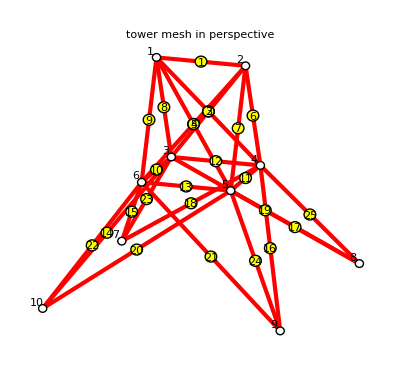

DOF Activity:

node | x-tag | y-tag | z-tag | x-value | y-value | z-value
1 |  0 |  0 |  0 |  1000 |  10000 | -5000
2 |  0 |  0 |  0 |  0 |  10000 | -5000
3 |  0 |  0 |  0 |  500 |  0 |  0
4 |  0 |  0 |  0 |  0 |  0 |  0
5 |  0 |  0 |  0 |  0 |  0 |  0
6 |  0 |  0 |  0 |  500 |  0 |  0
7 |  1 |  1 |  1 |  0 |  0 |  0
8 |  1 |  1 |  1 |  0 |  0 |  0
9 |  1 |  1 |  1 |  0 |  0 |  0
10 |  1 |  1 |  1 |  0 |  0 |  0

Computed node displacements:

node | x-displ | y-displ | z-displ
1 |  0.008515 |  0.349956 | -0.022128
2 |  0.031916 |  0.349956 | -0.032242
3 |  0.011530 | -0.009770 | -0.108526
4 | -0.004039 | -0.008781 | -0.115393
5 |  0.000448 | -0.005089 |  0.070508
6 |  0.007042 | -0.004100 |  0.077375
7 |  0.000000 |  0.000000 |  0.000000
8 |  0.000000 |  0.000000 |  0.000000
9 |  0.000000 |  0.000000 |  0.000000
10 |  0.000000 |  0.000000 |  0.000000

Node forces including reactions:

PaddedForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

General::stop: Further output of PaddedForm :: sigz will be suppressed during this calculation.

node | x-force | y-force | z-force
1 |  1000.0000 |  10000.0000 | -5000.0000
2 |  0.0000 |  10000.0000 | -5000.0000
3 |  500.0000 |  0.0000 |  0.0000
4 |  0.0000 |  0.0000 |  0.0000
5 |  0.0000 |  0.0000 |  0.0000
6 |  500.0000 |  0.0000 |  0.0000
7 |  9908.0000 | -6263.0000 |  11750.0000
8 | -10910.0000 | -7326.0000 |  13250.0000
9 |  5665.0000 | -2674.0000 | -6750.0000
10 | -6665.0000 | -3737.0000 | -8250.0000

Int Forces and Stresses:

PaddedForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

General::stop: Further output of PaddedForm :: sigz will be suppressed during this calculation.

elem | axial force | axial stress
1 |  103.0000 |  3120.0000
2 | -5996.0000 | -2976.0000
3 | -5126.0000 | -2544.0000
4 |  4077.0000 |  2023.0000
5 |  4947.0000 |  2455.0000
6 | -12720.0000 | -4504.0000
7 |  7522.0000 |  2665.0000
8 | -12000.0000 | -4252.0000
9 |  8234.0000 |  2917.0000
10 | -7.5590 | -755.9000
11 | -4.9230 | -492.3000
12 | -29.0600 | -2076.0000
13 | -12.3100 | -879.3000
14 | -3427.0000 | -3497.0000
15 |  2611.0000 |  2664.0000
16 | -3732.0000 | -3808.0000
17 |  2306.0000 |  2354.0000
18 | -6193.0000 | -3519.0000
19 | -6344.0000 | -3605.0000
20 |  3644.0000 |  2071.0000
21 |  3493.0000 |  1985.0000
22 |  10850.0000 |  4447.0000
23 | -13040.0000 | -5345.0000
24 |  9184.0000 |  3764.0000
25 | -14710.0000 | -6028.0000

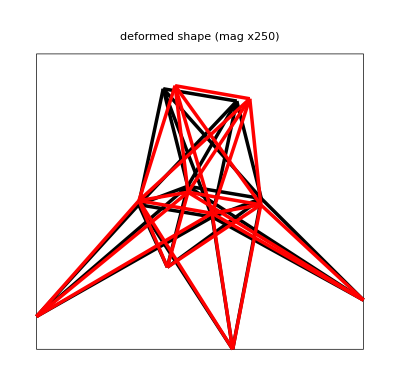

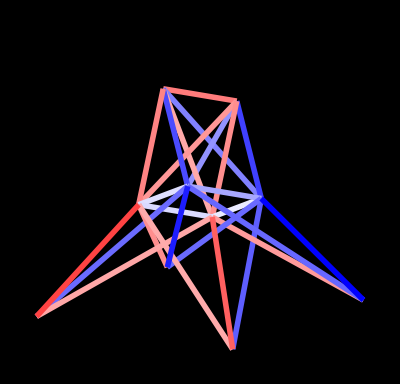

```mathematica
NodeCoordinates={{-37.5,0,200},     (*1*)
				{37.5,0,200},    	(*2*)
				{-37.5,37.5,100},	(*3*)
				{37.5,37.5,100},	(*4*)
				{37.5,-37.5,100},	(*5*)
				{-37.5,-37.5,100},	(*6*)
				{-100,100,0},		(*7*)
				{100,100,0},		(*8*)
				{100,-100,0},		(*9*)
				{-100,-100,0}		(*10*)
};
ElemNodes={{1,2},		(*1*)
		   {1,4},		(*2*)
		   {2,3},		(*3*)
		   {1,5},		(*4*)
		   {2,6},		(*5*)
		   {2,4},		(*6*)
           {2,5},		(*7*)
           {1,3},		(*8*)
           {1,6},		(*9*)
           {3,6},		(*10*)
           {4,5},		(*11*)
           {3,4},		(*12*)
           {5,6},		(*13*)
           {3,10},		(*14*)
           {6,7},		(*15*)
           {4,9},		(*16*)
           {5,8},		(*17*)
           {4,7},		(*18*)
           {3,8},		(*19*)
           {5,10},		(*20*)
           {6,9},		(*21*)
           {6,10},		(*22*)
           {3,7},		(*23*)
           {5,9},		(*24*)
           {4,8}		(*25*)
           };
PrintSpaceTrussNodeCoordinates[NodeCoordinates,"Node coordinates:",{}];            
numnod=Length[NodeCoordinates];  numele=Length[ElemNodes];
Em=10^7; 
ElemMaterials= Table[Em,{numele}]; 
ElemFabrications={ 	0.033,
				   	2.015,
				   	2.015,
				   	2.015,
				   	2.015,
				   	2.823,
				   	2.823,
				   	2.823,
				   	2.823,
				   	0.010,
				   	0.010,
				   	0.014,
				   	0.014,
				   	0.980,
				   	0.980,
				   	0.980,
				   	0.980,
				   	1.760,
				   	1.760,
				   	1.760,
				   	1.760,
				   	2.440,
				   	2.440,
				   	2.440,
				   	2.440};
PrintSpaceTrussElementData[ElemNodes,ElemMaterials,ElemFabrications,
           "Element data:",{}]; 
ProcessOptions= {True};

view={{0,0,1},{1,-3,1}};
labels={{True,0.014,-1.5,1.5},{True,0.020},{"Times",12,"Roman"}};
PlotSpaceTrussElementsAndNodes[NodeCoordinates,ElemNodes,
   "tower mesh in perspective",{view,-1,labels}];
  
NodeDOFTags=  Table[{0,0,0},{numnod}];
NodeDOFValues=Table[{0,0,0},{numnod}]; 
NodeDOFValues[[1]]={1000,10000,-5000}; 
NodeDOFValues[[2]]= {0,10000,-5000}; 
NodeDOFValues[[3]]={500,0,0};  
NodeDOFValues[[6]]={500,0,0}; 
NodeDOFTags[[7]]= {1,1,1};     (* fixed node 7,8,9,10 *)
NodeDOFTags[[8]]= {1,1,1};
NodeDOFTags[[9]]= {1,1,1};
NodeDOFTags[[10]]= {1,1,1};

PrintSpaceTrussFreedomActivity[NodeDOFTags,NodeDOFValues,
       "DOF Activity:",{}];

{NodeDisplacements,NodeForces,ElemForces,ElemStresses}=
   SpaceTrussSolution[ NodeCoordinates,ElemNodes,ElemMaterials,
   ElemFabrications,NodeDOFTags,NodeDOFValues,ProcessOptions ];
   
PrintSpaceTrussNodeDisplacements[NodeDisplacements,
      "Computed node displacements:",{}];
PrintSpaceTrussNodeForces[NodeForces,
      "Node forces including reactions:",{}];
PrintSpaceTrussElemForcesAndStresses[ElemForces,ElemStresses,
      "Int Forces and Stresses:",{}];
      
view={{0,0,1},{2,-3,1}};
box={{-100,100,0},{100,100,0},{100,-100,0},{-100,-100,0},
    {-100,100,200},{100,100,200},{100,-100,200},{-100,-100,200}};
PlotSpaceTrussDeformedShape[NodeCoordinates,ElemNodes,NodeDisplacements,
 {0,50},box,"deformed shape (mag x250)",{view,-1,{"black","red"}}];
PlotSpaceTrussStresses[NodeCoordinates,ElemNodes,ElemStresses,1,box,
 "axial stresses in truss members",{view,0,labels}];
```

```mathematica
SpaceTrussWeight[nodxyz_,elenod_,elefab_,specw_]:=Module[
{e,ni,nj,w=0,x1,x2,y1,y2,z1,z2,x21,y21,z21,
  numele=Length[elenod],LL},
  For [e=1,e<=numele,e++,  {ni,nj}=elenod[[e]]; 
       ncoor={nodxyz[[ni]],nodxyz[[nj]]};  
       {{x1,y1,z1},{x2,y2,z2}}=ncoor; 
       {x21,y21,z21}={x2-x1,y2-y1,z2-z1};LL=x21^2+y21^2+z21^2;
       w=w+Sqrt[LL]*elefab[[e]]*specw];
  Return[w]];    
    
w=SpaceTrussWeight[NodeCoordinates,ElemNodes,ElemFabrications,0.1]; 
Print["weight=",w];
```

weight=555.184